```mathematica
gray=RGBColor[0.7,0.7,0.7];
red=RGBColor[255/255,21/255,21/255];
SetDirectory[NotebookDirectory[]];
```

```mathematica
getTheoryData[pi_,pt_,pr_,pd_,n_]:=(
a=Import["FFM_2200_moments//output//diversity//diversity_pi_"<>ToString[pi]<>"_pt_"<>ToString[pt]<>"_pr_"<>ToString[pr]<>"_pd_"<>ToString[pd]<>"_.dat","Table"];
out={};
Do[
nnn=a[[i]][[-1]];
If[nnn<2&&i>61,Print["nnn error"<>ToString[i]]];
If[a[[i]][[2]]≠-1&&a[[i]][[1]]>61,AppendTo[out,{{a[[i]][[1]],a[[i]][[2*n]]},ErrorBar[a[[i]][[2*n + 1]]*√(nnn/(nnn-1))]}]],{i,1,1001}];
out
)
variance[x_]:=(μ=Mean[x];Sum[(x[[i]]-μ)^2,{i,1,Length[x]}]/(Length[x]))
```

## Fig A

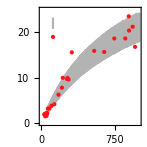

```mathematica
margins={0.9,0.5,1.2,0.4};
distance={0.6,0.6};
sizes={3*6/5,3*6/5};
fFigLegend[pi_,pt_,pr_,pd_]:=(
(*theory values*)
b=getTheoryData[pi,pt,pr,pd,10];

(*experimental values*)
fAll={};
f=Mean;
Do[
c=Import["chambers/c"<>ToString[j]<>".dat","List"];
AppendTo[fAll,{Total[c],N[f[c]]}]
,{j,1,21}];
Do[
c=Import["chambers/s"<>ToString[j]<>".dat","List"];
AppendTo[fAll,{Total[c],N[f[c]]}]
,{j,1,11}];

(*add legends*)
xLegend=120;
yLegend2=19;
yLegend1=0.12*25+yLegend2;
yError=0.05*25;
AppendTo[b,{{xLegend,yLegend1},ErrorBar[yError]}];
AppendTo[fAll,{xLegend,yLegend2}];

(*plots*)
p1=ErrorListPlot[b,PlotRange->{{0,1000},{0,0.75}},PlotStyle->gray];
p2=ListPlot[fAll,PlotRange->{0,4},PlotStyle->{red,PointSize->Medium}];
p3=Show[{p1,p2},Frame->True,Axes->False];

p4=plot[
{p3(*fit[gam,pMax],*)},
xTicks->{0,250,500,750,1000},
yTicks->{0,5,10,15,20,25},
tickLength->0.12,
plotRange->{{0,1000},{0,25}},
plotDimensions->sizes,
plotMargins->margins,
plotLabels->{
Row[{Style["Cell number"]}],
Row[{Style["Mean μ"]}]},
labelsDistance->{0.5,0.65},
plotTitle->True,
titleText->Row[{Style[""]}],
titleDistance->0.25,
fontMain->7,
fontName->"Helvetica"
]
)
figA=fFigLegend["0.0001",0.7,"0.158114",0.026];
t1=Style["Theory",FontSize->6,FontFamily->"Helvetica",gray];
t2=Style["Experiment",FontSize->6,FontFamily->"Helvetica",red];
ddx=0.2;
FigA=figure[6,5,
elements->{figA,t1,t2},
elementCoordinates->{
{0,0},
{1.2+3*6/5*(xLegend/1000)+ddx,-0.5-(25-yLegend1)/25*3*6/5},
{1.2+3*6/5*(xLegend/1000)+ddx,-0.5-(25-yLegend2)/25*3*6/5}
},
yCenteredElements->{2,3}]
```

## Fig B-D

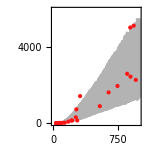

```mathematica
margins={0.9,0.5,1.2,0.4};
distance={0.6,0.6};
sizes={3*6/5,3*6/5};
fFig[pi_,pt_,pr_,pd_,f_,n_,yLabel_,yLabelDistance_,yRange_,yTicksList_]:=(
(*theory values*)
b=getTheoryData[pi,pt,pr,pd,n];

(*experimental values*)
fAll={};
Do[
c=Import["chambers/c"<>ToString[j]<>".dat","List"];
AppendTo[fAll,{Total[c],N[f[c]]}]
,{j,1,21}];
Do[
c=Import["chambers/s"<>ToString[j]<>".dat","List"];
AppendTo[fAll,{Total[c],N[f[c]]}]
,{j,1,11}];

(*plots*)
p1=ErrorListPlot[b,PlotRange->{{0,1000},yRange},PlotStyle->gray];
p2=ListPlot[fAll,PlotRange->{{0,1000},yRange},PlotStyle->{red,PointSize->Medium}];
p3=Show[{p1,p2},Frame->True,Axes->False];

p4=plot[
{p3(*fit[gam,pMax],*)},
xTicks->{0,250,500,750,1000},
yTicks->yTicksList,
tickLength->0.12,
plotRange->{{0,1000},yRange},
plotDimensions->{3*6/5,3*6/5},
plotMargins->{0.9,0.5,1.2,0.4},
plotLabels->{
Row[{Style["Cell number"]}],
yLabel},
labelsDistance->{0.5,yLabelDistance},
plotTitle->True,
titleText->Row[{Style[""]}],
titleDistance->0.25,
fontMain->7,
fontName->"Helvetica"
]
)

FigB=fFig["0.0001",0.7,"0.158114",0.026,
variance,
11,
Row[{
Style["Variance "],Superscript[Style["σ"],Style["2",FontSize->6]]
}],
0.95,
{0,6000},
{0,2000,4000,6000}
]
```

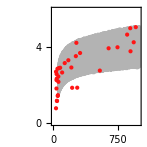

```mathematica
FigC=fFig["0.0001",0.7,"0.158114",0.026,
Skewness,
12,
Row[{
Style["Skewness "],Subscript[Style["μ̃"],Style["3",FontSize->5]]
}],
0.55,
{0,6},
{0,2,4,6}
]
```

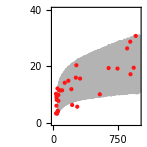

```mathematica
FigD=fFig["0.0001",0.7,"0.158114",0.026,
Kurtosis,
13,
Row[{
Style["Kurtosis "],Subscript[Style["μ̃"],Style["4",FontSize->6]]
}],
0.65,
{0,40},
{0,10,20,30,40}
]
```

## Figure

```mathematica
fLegend=6;
t1=Row[{Subscript[Style["p",Italic,FontFamily->"Arial",FontSize->6],Style["i",FontFamily->"Arial",FontSize->4]],Style[StringJoin[" = 0.0001"],FontFamily->"Arial",FontSize->fLegend]}];
t2=Row[{Subscript[Style["p",Italic,FontFamily->"Arial",FontSize->6],Style["t",FontFamily->"Arial",FontSize->4]],Style[StringJoin[" = 0.7"],FontFamily->"Arial",FontSize->fLegend]}];
t3=Row[{Subscript[Style["p",Italic,FontFamily->"Arial",FontSize->6],Style["r",FontFamily->"Arial",FontSize->4]],Style[" = 0.1581",FontFamily->"Arial",FontSize->fLegend]}];
t4=Row[{Subscript[Style["p",Italic,FontFamily->"Arial",FontSize->6],Style["c",FontFamily->"Arial",FontSize->4]],Style[StringJoin[" = 0.026"],FontFamily->"Arial",FontSize->fLegend]}];
center={0.1,0};
dxx={0,-0.29};
l1a=figure[
1.8,
1.4,
elements->{t1,t2,t3,t4},
elementCoordinates->{center,center+1*dxx,center+2*dxx,center+3*dxx}]
```

-Graphics-

-0.1

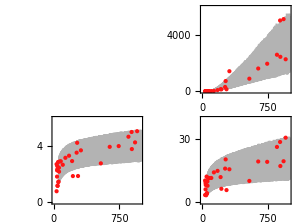

```mathematica
x0=0;
y0=0;
dx=5.2;
dy=-4.7;
dy0=-0.1;
dxLet=0.;
dx0=-0.1
FigED7=figure[
10.5,
9.5,
elements->{FigA,FigB,FigC,FigD,l1a},
elementCoordinates->{
{0*dx+dx0,0*dy-dy0},{1*dx+dx0,0*dy-dy0},
{0*dx+dx0,1*dy-dy0},{1*dx+dx0,1*dy-dy0},{0*dx+dx0+margins[[3]]+sizes[[1]]*5/8-0.4,-5.8-dy0-dy-1.1-0.3}},
letters->{
Style["a",FontFamily->"Helvetica",FontSize->8,Bold],
Style["b",FontFamily->"Helvetica",FontSize->8,Bold],
Style["c",FontFamily->"Helvetica",FontSize->8,Bold],
Style["d",FontFamily->"Helvetica",FontSize->8,Bold]
},
letterCoordinates->{{0*dx+dxLet,0*dy},{1*dx+dxLet,0*dy},{0*dx+dxLet,1*dy},{1*dx+dxLet,1*dy}},
(*letters->{"A","B","C","D","E","F","G","H"}(*list of letters for the figure elements, as strings, e.g. {"a)","b)","c)"}, or {"A","B"}*),
letterCoordinates->{{0*dx,0*dy},{1*dx,0*dy},{2*dx,0*dy},{0*dx,1*dy},{1*dx,1*dy},{2*dx,1*dy},{0.5*dx,2*dy},{1.5*dx,2*dy}}(**),*)
centeredElements->{10}]
```

```mathematica
Export["figs//SYS_ED_Fig7.pdf",FigED7]
```

figs//SYS_ED_Fig7.pdf